# John Lewis, 904082686, johnlewis1928@gmail.com, HW 2

```mathematica
(*Problem 1*)
Remove["Global`*"]
DSolve[{x''[t]-a==0,x'[0]==v0,x[0]==x0},x[t],t] //Simplify
```

{{x[t]→(a t^2)/2+t v0+x0}}

```mathematica
(*Problem 2*)
Remove["Global`*"]
(DSolve[{{2 k x[t]-k y[t]+m x''[t]==0,x'[0]==0,y'[0]==0,x[0]==0,y[0]==a},{-(k x[t])+2 k y[t]+m y''[t]==0,x'[0]==0,y'[0]==0,x[0]==0,y[0]==a}},{x[t],y[t]},t]  //Simplify)
```

{{x[t]→1/2 a (Cos[(√k t)/(√m)]-Cos[(√3 √k t)/(√m)]),y[t]→1/2 a (Cos[(√k t)/(√m)]+Cos[(√3 √k t)/(√m)])}}

(300.-300. ⅇ^(-k t))/k

(9.8+ⅇ^(-1. k t) (-9.8-519.615 k)+k (519.615-9.8 t))/k^2

(1.+53.022 k+1. ProductLog[6.72544×10^-16 ⅇ^(-53.022 k) (-5.46997×10^14-2.90029×10^16 k)])/k

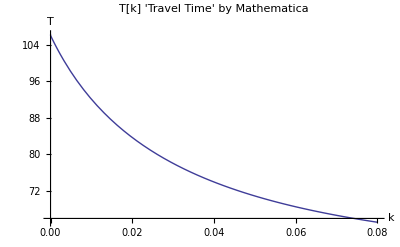

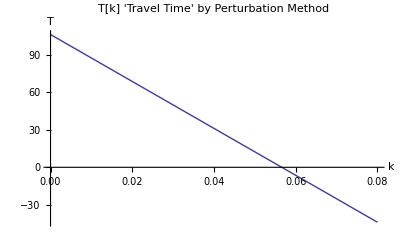

```mathematica
(*Problem 3*)
Remove["Global`*"]
g=9.8;
U=600 Cos[60 Degree];
V=600 Sin[60 Degree];
soln1=DSolve[{m x''[t]==-k m x'[t],m y''[t]==-k m y'[t]-m g,x[0]==y[0]==0,x'[0]==U,y'[0]==V},{x[t],y[t]},t] //FullSimplify;
x[t_]=x[t]/.soln1[[1]]
y[t_]=y[t]/.soln1[[1]]
soln2=Solve[y[T[k]]==0,T[k]] //Quiet;
T[k_]=T[k]/.soln2[[1]]
Plot[{T[k]},{k,0,.08}, PlotLabel->"T[k] 'Travel Time' by Mathematica", AxesLabel->{"k","T"}]
Plot[(2 V/g)(1-((k V)/(3 g))),{k,0,.08},PlotLabel->"T[k] 'Travel Time' by Perturbation Method", AxesLabel->{"k","T"}]
```

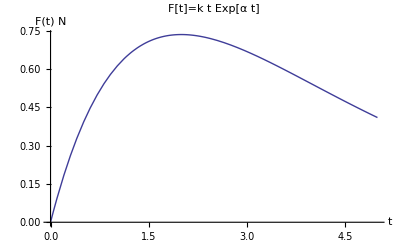

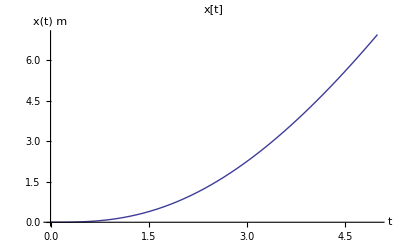

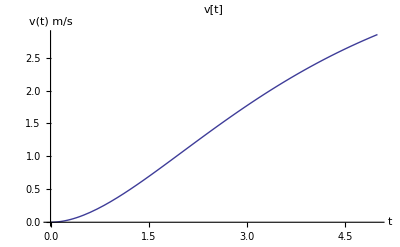

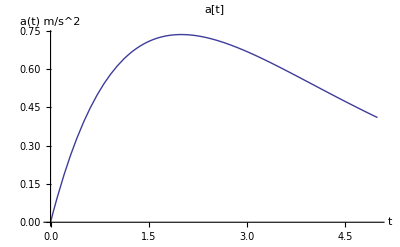

```mathematica
(*Problem 4*)
Remove["Global`*"];
m=1;
k=1;
α=.5;
F[t_]=k t Exp[-α t];
soln=DSolve[{m x''[t]-F[t]==0,x'[0]==0,x[0]==0},x[t],t] //FullSimplify;
x[t_]=x[t]/.soln[[1]] //FullSimplify;
v[t_]=x'[t] //FullSimplify;
a[t_]=x''[t] //FullSimplify;
Plot[F[t],{t,0,5},PlotLabel->"F[t]=k t Exp[α t]",AxesLabel->{"t","F(t) N"}]
Plot[x[t],{t,0,5},PlotLabel->"x[t]",AxesLabel->{"t","x(t) m" }]
Plot[v[t],{t,0,5},PlotLabel->"v[t]",AxesLabel->{"t","v(t) m/s"}]
Plot[a[t],{t,0,5},PlotLabel->"a[t]",AxesLabel->{"t","a(t) m/s^2"}]
```

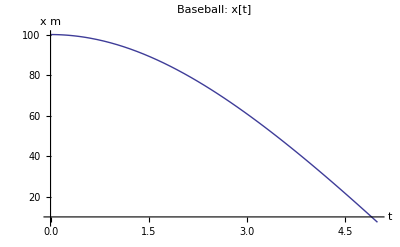

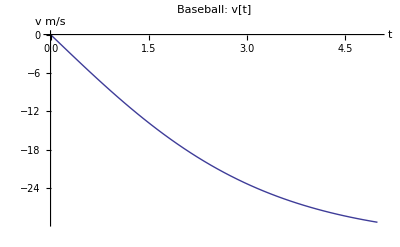

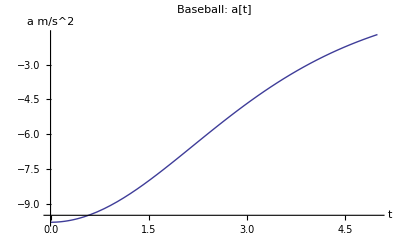

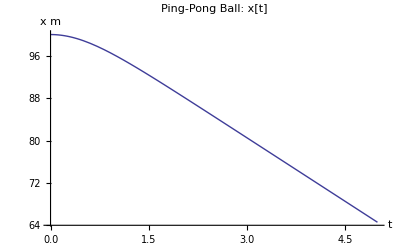

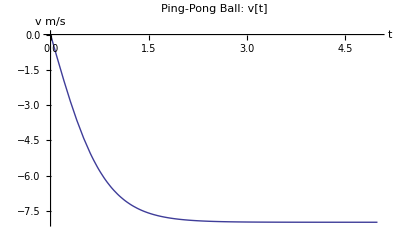

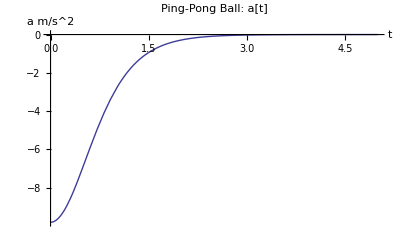

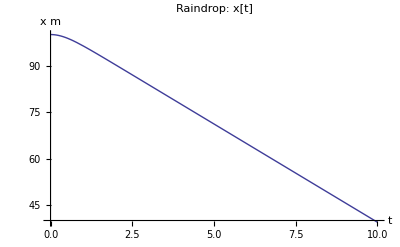

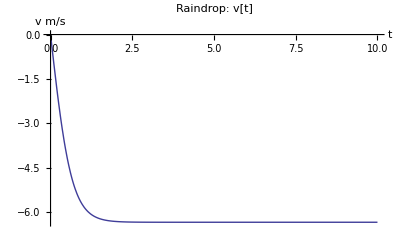

```mathematica
(*Problem 5*)
Remove["Global`*"]
g=9.8;cw=.5;ρ=1.3;
Fg:=m g;
W:=   .5 cw ρ (Pi r^2) (x'[t]^2);
soln=Quiet[DSolve[{ m x''[t]==-Fg +W,x[0]==100,x'[0]==0},x[t],t]  //Simplify];
x[t_]=x[t]/.soln[[1]];
v[t_]=D[x[t],t];
a[t_]=D[v[t],t];
(*Baseball*)
{m,r}={.145,.0366};
Plot[x[t],{t,0,5}, PlotLabel->"Baseball: x[t]",AxesLabel->{"t","x m"},PlotRange->All]
Plot[v[t],{t,0,5}, PlotLabel->"Baseball: v[t]",AxesLabel->{"t","v m/s"},PlotRange->All]
Plot[a[t],{t,0,5}, PlotLabel->"Baseball: a[t]",AxesLabel->{"t","a m/s^2"},PlotRange->All]
(*Ping-Pong Ball*)
{m,r}={.0024,.019};
Plot[x[t],{t,0,5}, PlotLabel->"Ping-Pong Ball: x[t]",AxesLabel->{"t","x m"},PlotRange->All]
Plot[v[t],{t,0,5}, PlotLabel->"Ping-Pong Ball: v[t]",AxesLabel->{"t","v m/s"},PlotRange->All]
Plot[a[t],{t,0,5}, PlotLabel->"Ping-Pong Ball: a[t]",AxesLabel->{"t","a m/s^2"},PlotRange->All]
(*Raindrop of radius .003, mass (4/3) π r^2*)
{m,r}={(4/3) Pi .003^2 ,.003};
Plot[x[t],{t,0,10}, PlotLabel->"Raindrop: x[t]",AxesLabel->{"t","x m"},PlotRange->All]
Plot[v[t],{t,0,10}, PlotLabel->"Raindrop: v[t]",AxesLabel->{"t","v m/s"},PlotRange->All]
Plot[a[t],{t,0,10}, PlotLabel->"Raindrop: a[t]",AxesLabel->{"t","a m/s^2"},PlotRange->All]
(*They all reach terminal velocity---The baseball can be thrown further because the resistive force has less effect on it that the ping pong ball*)
```

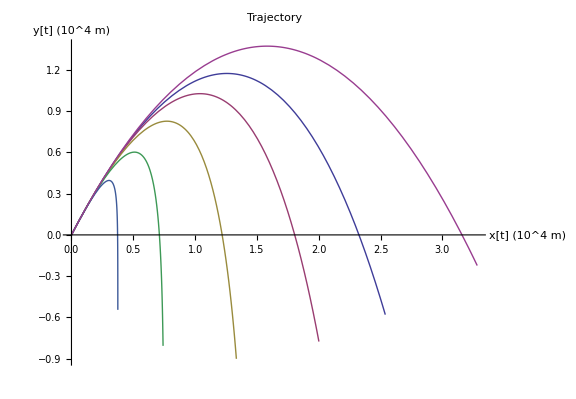

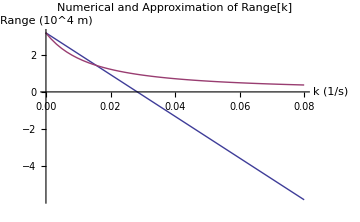

```mathematica
(*Problem 6*)
Remove["Global`*"]
Needs["PlotLegends`"]
ScalingFactor=10^4;
g=9.8;V=600 Sin[Pi/3];U=600 Cos[Pi/3];
y[t_,k_]=((-g t/k) + (((k V)+g)/(k^2))(1-Exp[-k t]))/(ScalingFactor);
x[t_,k_]=((U/k)(1-Exp[-k t]))/(ScalingFactor);
ParametricPlot[{{x[t,.005],y[t,.005]},{x[t,.01],y[t,.01]},{x[t,.02],y[t,.02]},{x[t,.04],y[t,.04]},{x[t,.08],y[t,.08]},{x[t,10^-4],y[t,10^-4]}},{t,0,110}, PlotLabel->"Trajectory ",AxesLabel->{"x[t] (10^4 m)","y[t] (10^4 m)"},PlotLegend->{"k=.005","k=.01","k=.02","k=.04","k=.08", "k~0"},ImageSize->Large]
R=((600^2)/g) Sin[Pi/1.5];
range[k_]=R (1-(2 k V/(3 g)));
T[k_]=T[k]/.Quiet[Solve[T[k]==((k V +g)/(g k))*(1-Exp[- k T[k]]),T[k]]][[1]];
Plot[{range[k]/ScalingFactor,x[T[k],k]},{k,0,.08},PlotLabel->"Numerical and Approximation of Range[k]",PlotLegend->{"Approximation","Numerical"},AxesLabel->{"k (1/s)","Range (10^4 m)"}, ImageSize->Medium]
```